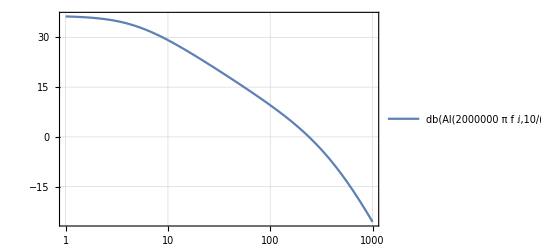

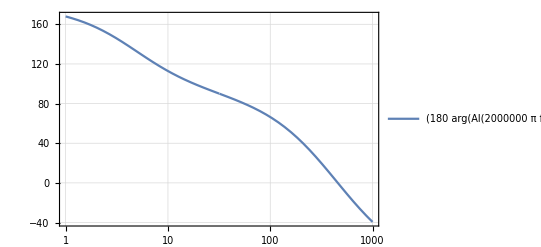

```mathematica
-Graphics-;
Z[s_]:=(40*10^3)/((1+s/(30*10^6))(1+s/(2000*10^6)));
Rf=511;Rg=255;Rb=29;
Al[s_,Cg_]:=-Z[s]/(Rf+Rb(1+(Rf(1+s Rg Cg))/Rg));
db[a_]:=20*Log10[Abs[a]];
LogLinearPlot[db[Al[2000000*π*f*ⅈ,10*10^-12]],{f,1,1000},PlotTheme->"Detailed"]
LogLinearPlot[180/π*Arg[Al[2000000*π*f*ⅈ,10*10^-12]],{f,1,1000},PlotTheme->"Detailed"]
```